```mathematica
(* Load the LatticeGasMC package.  The path is resolved for both contexts this
   notebook has to run in: the Wolfram front end, where NotebookDirectory[] is
   defined, and the headless kernel the MyST wolfram plugin drives, where it is
   not (wolframscript runs from the book root instead). *)
latticeGasLibraryPath = SelectFirst[
   {Quiet@Check[
     FileNameJoin[{NotebookDirectory[], "library", "LatticeGasMC.wl"}], $Failed],
    FileNameJoin[{Directory[], "notebooks", "library", "LatticeGasMC.wl"}],
    FileNameJoin[{Directory[], "library", "LatticeGasMC.wl"}]},
   StringQ[#] && FileExistsQ[#] &,
   $Failed];
If[latticeGasLibraryPath === $Failed,
  Print["LatticeGasMC.wl not found; looked next to the notebook and under ",
    Directory[]];
  Abort[],
  Get[latticeGasLibraryPath]];
```

```mathematica
deltaMuValues = Range[-2.0, 2.0, 0.2];
```

```mathematica
orangeFraction[config_] := Module[{counts = latticeGasSpeciesCounts[config]},
   counts["orange"]/N[counts["orange"] + counts["blue"]]];
```

```mathematica
Options[sweepBranch]= {"Metropolis Iterations"->2 10^6};
sweepBranch[deltas_, OptionsPattern[{latticeGasBulkExchangeSweep,sweepBranch}]] := Module[{config, branch = <||>, configurations=<||>},
   config = latticeGasRandomConfiguration[64, 64, 1850, 1850];
   Do[
    {config, statistics} = 
latticeGasBulkExchangeSweep[config, OptionValue["Metropolis Iterations"],
       "energyNearest" -> OptionValue["energyNearest"],
"energyNextNearest" -> OptionValue["energyNextNearest"],
 "muOrange" -> 1. + deltaMu/2 ,
"muBlue" -> 1. - deltaMu/2.,
 "inverseTemperature" -> OptionValue["inverseTemperature"],
"exchangeProbability"->OptionValue["exchangeProbability"]];
AssociateTo[configurations, deltaMu->config];
    AssociateTo[branch, deltaMu->orangeFraction[config]],
    {deltaMu, deltas}];
 {  branch,configurations}];
```

```mathematica
Options[sweepBranchWithNuclei]= {"Metropolis Iterations"->2 10^6};
sweepBranchWithNuclei[deltas_, OptionsPattern[{latticeGasBulkExchangeSweep,sweepBranchWithNuclei}]] := 
 Module[{config,origConfig, branch = <||>, configurations=<||>, statistics},
   config =origConfig= ArrayPad[
Table[
Which[(i-35)^2 + j^2 <= 50,1,(i+35)^2 + j^2 <= 50,-1,True,0 ],{i,-100,100},{j,-100,100}],1
];
   Do[
   {config,statistics}= latticeGasBulkExchangeSweep[config, OptionValue["Metropolis Iterations"],
       "energyNearest" -> OptionValue["energyNearest"],
"energyNextNearest" -> OptionValue["energyNextNearest"],
  "muOrange" -> 1. + deltaMu/2 ,
"muBlue" -> 1. - deltaMu/2.,
 "inverseTemperature" -> OptionValue["inverseTemperature"],
"exchangeProbability"->OptionValue["exchangeProbability"]];
AssociateTo[configurations, deltaMu->config];
    AssociateTo[branch, deltaMu->orangeFraction[config]];
config= origConfig,
    {deltaMu, deltas}];
 {  branch,configurations}];
```

## Global and Local Equilibrium: Nucleation and Hysteresis in the Lattice Gas Metropolis Model

Each value of  has an equilibrium concentration.

We probe the concentrations by iteratively finding the concentration as we sweep along values of . 

In this case, we will probe the behavior for the case where there are two disordered phases separated by a miscibility gap.  This is the classic case of a phase diagram associated with spinodal decomposition.
-Graphics-

However, because the appearance of a new phase comes with a surface energy penalty, it is possible that the equilibrium phase will not appear (i.e., if there is a nucleation barrier.

This notebook explores this behavior.

### Concentration versus starting from an uniform random configuration

The function sweepBranch takes a list of ’s  iterates at each  enough iterations to have confidence the system has reached a (local) equilibrium.  

After each equilibrium is found, the system uses the last configuration for the previous  as a starting point—akin to doing a slow experimental sweep with .

The function returns an  of final concentrations and final configurations.

For example:

```mathematica
{concetrations, configurations}=sweepBranch[{0.2,0.9},
"Metropolis Iterations"->2 10^6,
 "energyNearest" -> -1.0,
 "energyNextNearest" -> -0.4,
"inverseTemperature" -> 1/1.2];
```

```mathematica
concetrations
```

<|0.2→0.999262,0.9→1.|>

```mathematica
(* #| label: fig:demo-lattice *)
drawLattice[configurations[0.2],ImageSize->400]
```

-Graphics-

We will sweep over these values of :

```mathematica
deltaMuValues
```

{-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,1.11022×10^-16,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

First, we start from the negative values and increment to towards positive :

```mathematica
{upBranch, upConfigurations} = sweepBranch[deltaMuValues,
"Metropolis Iterations"->2 10^6,
 "energyNearest" -> -1.0,
 "energyNextNearest" -> -0.4,
"inverseTemperature" -> 1/1.2
];
```

Next, we start from the positive values and increment to towards negative :

```mathematica
{downBranch, downConfigurations}= sweepBranch[Reverse[deltaMuValues],"Metropolis Iterations"->2 10^6,
 "energyNearest" -> -1.0,
 "energyNextNearest" -> -0.4,
"inverseTemperature" -> 1/1.2];
```

Visualizing:

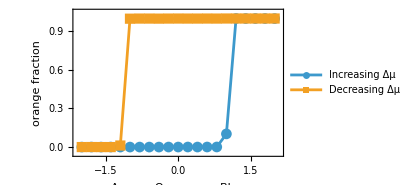

```mathematica
(* #| label: fig:hysteresis-random *)
llp =ListLinePlot[{upBranch, downBranch}, PlotMarkers -> Automatic,
   Frame -> True,
   FrameLabel -> {"Δμ = μ_Orange - μ_Blue", "orange fraction"},
   PlotLegends -> {"Increasing Δμ", "Decreasing Δμ"},
   PlotRange -> {{-2.1, 2.1}, {-0.05, 1.05}}, ImageSize -> 300,BaseStyle->{FontSize->16}]
```

Observe that there are two concentrations for a range of .  The system cannot be in a global equilibrium.  We can visualize why:

The function sweepBranch takes a list of ’s  iterates at each  enough iterations to have confidence the system has reached a (local) equilibrium.

```mathematica
(* #| label: fig:sweep-explorer-random *)
DynamicModule[
{micro =drawLattice[downConfigurations[[-1]],ImageSize->400],
inset= Show[llp,Graphics[{Black,PointSize[0.05],Point[upBranch[[-1]]]}],ImageSize->300],
upBranchPairs= Transpose[{Keys[upBranch],Values[upBranch]}],
downBranchPairs= Transpose[{Keys[downBranch],Values[downBranch]}]
},
Manipulate[
Which[
direction=="down",
micro =drawLattice[downConfigurations[[i]],ImageSize->200];
inset = Show[llp,Graphics[{Black,PointSize[0.05],Point[downBranchPairs[[i]]]}],ImageSize->300];,
True,
micro =drawLattice[upConfigurations[[-i]],ImageSize->200];
inset = Show[llp,Graphics[{Black,PointSize[0.05],Point[upBranchPairs[[-i]]]}],ImageSize->300]
];
GraphicsRow[{micro,inset}],
{i,1,Length[downConfigurations],1},
{{direction,"down"},{"down","up"}},
SaveDefinitions->True
]
]
```

Apparently, the system needs to overcome a nucleation barrier to achieve global equilibrium.

### Concentration versus starting from a configuration containing a “nucleation seed””

The function sweepBranchWithNuclei  is similar to sweepBranch , except that it uses a “seed configuration at each new value of . At each  ., the configuration looks like:

```mathematica
(* #| label: fig:seed-configuration *)
drawLattice[
ArrayPad[
Table[
Which[(i-35)^2 + j^2 <= 50,1,(i+35)^2 + j^2 <= 50,-1,True,0 ],{i,-100,100},{j,-100,100}],1
]]
```

-Graphics-

So, there is a small seed to help the system get over the nucleation barrier.

Here is the experiment:

Increasing :

```mathematica
{upBranchWithNuclei, upConfigurationsWithNuclei} = sweepBranchWithNuclei[deltaMuValues,
"Metropolis Iterations"->2 10^6,
 "energyNearest" -> -1.0,
 "energyNextNearest" -> -0.4,
"inverseTemperature" -> 1/1.2
];
```

Decreasing :

```mathematica
{downBranchWithNuclei, downConfigurationsWithNuclei}= sweepBranchWithNuclei[Reverse[deltaMuValues],"Metropolis Iterations"->2 10^6,
 "energyNearest" -> -1.0,
 "energyNextNearest" -> -0.4,
"inverseTemperature" -> 1/1.2];
```

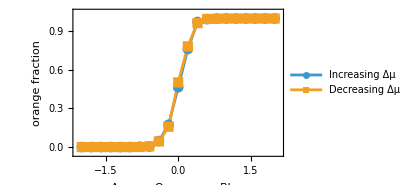

```mathematica
(* #| label: fig:hysteresis-seeded *)
llpWithNuclei=ListLinePlot[{upBranchWithNuclei, downBranchWithNuclei}, PlotMarkers -> Automatic,
   Frame -> True,
   FrameLabel -> {"Δμ = μ_Orange - μ_Blue", "orange fraction"},
   PlotLegends -> {"Increasing Δμ", "Decreasing Δμ"},
   PlotRange -> {{-2.1, 2.1}, {-0.05, 1.05}}, ImageSize -> 300,BaseStyle->{FontSize->16}]
```

```mathematica
(* #| label: fig:sweep-explorer-seeded *)
DynamicModule[
{micro =latticeGasConfigurationPlot[downConfigurationsWithNuclei[[-1]],ImageSize->400],
inset= Show[llpWithNuclei,Graphics[{Black,PointSize[0.05],Point[upBranchWithNuclei[[-1]]]}],ImageSize->300],
upBranchPairs= Transpose[{Keys[upBranchWithNuclei],Values[upBranchWithNuclei]}],
downBranchPairs= Transpose[{Keys[downBranchWithNuclei],Values[downBranchWithNuclei]}]
},
Manipulate[
Which[
direction=="down",
micro =latticeGasConfigurationPlot[downConfigurationsWithNuclei[[i]],ImageSize->200];
inset = Show[llpWithNuclei,Graphics[{Black,PointSize[0.05],Point[downBranchPairs[[i]]]}],ImageSize->300];,
True,
micro =latticeGasConfigurationPlot[upConfigurationsWithNuclei[[-i]],ImageSize->200];
inset = Show[llpWithNuclei,Graphics[{Black,PointSize[0.05],Point[upBranchPairs[[-i]]]}],ImageSize->300]
];
GraphicsRow[{micro,inset}],
{i,1,Length[downConfigurationsWithNuclei],1},
{{direction,"down"},{"down","up"}},
SaveDefinitions->True
]
]
```

It is expected that the sigmoid curve would become sharper with more Metropolis iterations and a larger system.